```mathematica
csvFiles=FileNames["*.csv",NotebookDirectory[]];
```

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"cpi.csv"}],CharacterEncoding->"UTF-8"]
```

{{Annual Consumer Price Index for the United States},{Source: <a href="http://www.measuringworth.com/datasets/uscpi/">Measuring Worth</a>},{Lawrence H. Officer, “The Annual Consumer Price Index for the United States, 1774- 2010,” MeasuringWorth, 2011 URL: <a href="http://www.measuringworth.com/uscpi/">http://www.measuringworth.com/uscpi/</a>},{From 1982 on, the data is from the Bureau of Labor Statistics. MeasuringWorth provides a <a href="http://www.measuringworth.com/docs/cpistudyrev.pdf">62-page technical report</a> on how prior years were calculated.},{# Year, CPI (100 1983 dollars)},{1774,7.82},{1775,7.41},{1776,8.46},{1777,10.31},{1778,13.38},{1779,11.84},{1780,13.29},{1781,10.72},{1782,11.76},{1783,10.31},{1784,9.91},{1785,9.43},{1786,9.19},{1787,9.02},{1788,8.62},{1789,8.54},{1790,8.86},{1791,9.1},{1792,9.27},{1793,9.59},{1794,10.64},{1795,12.17},{1796,12.81},{1797,12.33},{1798,11.92},{1799,11.92},{1800,12.17},{1801,12.33},{1802,10.39},{1803,10.96},{1804,11.44},{1805,11.36},{1806,11.84},{1807,11.2},{1808,12.17},{1809,11.92},{1810,11.92},{1811,12.73},{1812,12.89},{1813,15.47},{1814,17.},{1815,14.91},{1816,13.62},{1817,12.89},{1818,12.33},{1819,12.33},{1820,11.36},{1821,10.96},{1822,11.36},{1823,10.15},{1824,9.35},{1825,9.59},{1826,9.59},{1827,9.67},{1828,9.19},{1829,9.02},{1830,8.94},{1831,8.38},{1832,8.3},{1833,8.14},{1834,8.3},{1835,8.54},{1836,9.02},{1837,9.27},{1838,9.02},{1839,9.02},{1840,8.38},{1841,8.46},{1842,7.9},{1843,7.17},{1844,7.25},{1845,7.33},{1846,7.41},{1847,7.98},{1848,7.65},{1849,7.41},{1850,7.57},{1851,7.41},{1852,7.49},{1853,7.49},{1854,8.14},{1855,8.38},{1856,8.22},{1857,8.46},{1858,7.98},{1859,8.06},{1860,8.06},{1861,8.54},{1862,9.75},{1863,12.17},{1864,15.23},{1865,15.79},{1866,15.39},{1867,14.34},{1868,13.78},{1869,13.21},{1870,12.65},{1871,11.84},{1872,11.84},{1873,11.6},{1874,11.04},{1875,10.64},{1876,10.39},{1877,10.15},{1878,9.67},{1879,9.67},{1880,9.91},{1881,9.91},{1882,9.91},{1883,9.71},{1884,9.51},{1885,9.32},{1886,9.12},{1887,9.22},{1888,9.22},{1889,8.92},{1890,8.82},{1891,8.82},{1892,8.82},{1893,8.72},{1894,8.34},{1895,8.14},{1896,8.14},{1897,8.04},{1898,8.04},{1899,8.04},{1900,8.14},{1901,8.24},{1902,8.34},{1903,8.53},{1904,8.63},{1905,8.53},{1906,8.72},{1907,9.11},{1908,8.92},{1909,8.82},{1910,9.21},{1911,9.21},{1912,9.4},{1913,9.6},{1914,9.69},{1915,9.74},{1916,10.64},{1917,12.82},{1918,15.06},{1919,17.3},{1920,20.04},{1921,17.9},{1922,16.77},{1923,17.07},{1924,17.1},{1925,17.53},{1926,17.7},{1927,17.37},{1928,17.13},{1929,17.13},{1930,16.7},{1931,15.23},{1932,13.66},{1933,12.96},{1934,13.39},{1935,13.73},{1936,13.86},{1937,14.36},{1938,14.09},{1939,13.89},{1940,14.03},{1941,14.73},{1942,16.3},{1943,17.3},{1944,17.6},{1945,18.},{1946,19.54},{1947,22.34},{1948,24.08},{1949,23.85},{1950,24.08},{1951,25.98},{1952,26.55},{1953,26.75},{1954,26.88},{1955,26.78},{1956,27.18},{1957,28.15},{1958,28.92},{1959,29.16},{1960,29.62},{1961,29.92},{1962,30.26},{1963,30.62},{1964,31.03},{1965,31.56},{1966,32.46},{1967,33.4},{1968,34.8},{1969,36.67},{1970,38.84},{1971,40.51},{1972,41.85},{1973,44.45},{1974,49.33},{1975,53.84},{1976,56.94},{1977,60.61},{1978,65.22},{1979,72.57},{1980,82.38},{1981,90.93},{1982,96.5},{1983,99.6},{1984,103.9},{1985,107.6},{1986,109.6},{1987,113.6},{1988,118.3},{1989,124.},{1990,130.7},{1991,136.2},{1992,140.3},{1993,144.5},{1994,148.2},{1995,152.4},{1996,156.9},{1997,160.5},{1998,163.},{1999,166.6},{2000,172.2},{2001,177.1},{2002,179.9},{2003,184.},{2004,188.9},{2005,195.3},{2006,201.6},{2007,207.34},{2008,215.3},{2009,214.54},{2010,218.06}}

```mathematica
data⟦6;;,2⟧
```

{7.82,7.41,8.46,10.31,13.38,11.84,13.29,10.72,11.76,10.31,9.91,9.43,9.19,9.02,8.62,8.54,8.86,9.1,9.27,9.59,10.64,12.17,12.81,12.33,11.92,11.92,12.17,12.33,10.39,10.96,11.44,11.36,11.84,11.2,12.17,11.92,11.92,12.73,12.89,15.47,17.,14.91,13.62,12.89,12.33,12.33,11.36,10.96,11.36,10.15,9.35,9.59,9.59,9.67,9.19,9.02,8.94,8.38,8.3,8.14,8.3,8.54,9.02,9.27,9.02,9.02,8.38,8.46,7.9,7.17,7.25,7.33,7.41,7.98,7.65,7.41,7.57,7.41,7.49,7.49,8.14,8.38,8.22,8.46,7.98,8.06,8.06,8.54,9.75,12.17,15.23,15.79,15.39,14.34,13.78,13.21,12.65,11.84,11.84,11.6,11.04,10.64,10.39,10.15,9.67,9.67,9.91,9.91,9.91,9.71,9.51,9.32,9.12,9.22,9.22,8.92,8.82,8.82,8.82,8.72,8.34,8.14,8.14,8.04,8.04,8.04,8.14,8.24,8.34,8.53,8.63,8.53,8.72,9.11,8.92,8.82,9.21,9.21,9.4,9.6,9.69,9.74,10.64,12.82,15.06,17.3,20.04,17.9,16.77,17.07,17.1,17.53,17.7,17.37,17.13,17.13,16.7,15.23,13.66,12.96,13.39,13.73,13.86,14.36,14.09,13.89,14.03,14.73,16.3,17.3,17.6,18.,19.54,22.34,24.08,23.85,24.08,25.98,26.55,26.75,26.88,26.78,27.18,28.15,28.92,29.16,29.62,29.92,30.26,30.62,31.03,31.56,32.46,33.4,34.8,36.67,38.84,40.51,41.85,44.45,49.33,53.84,56.94,60.61,65.22,72.57,82.38,90.93,96.5,99.6,103.9,107.6,109.6,113.6,118.3,124.,130.7,136.2,140.3,144.5,148.2,152.4,156.9,160.5,163.,166.6,172.2,177.1,179.9,184.,188.9,195.3,201.6,207.34,215.3,214.54,218.06}

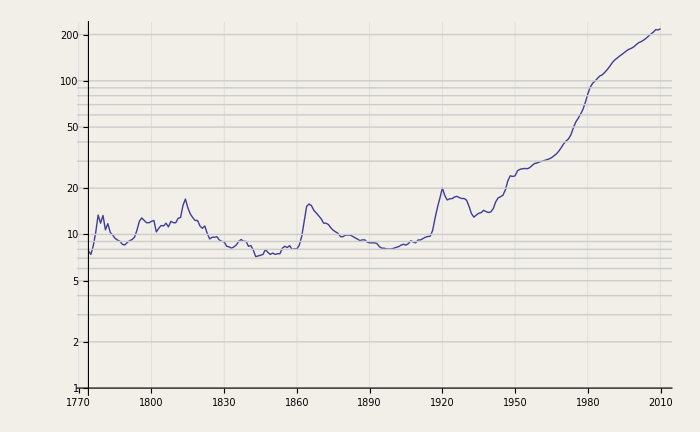

```mathematica
cpi=ListLogPlot[data⟦6;;⟧,Joined->True,GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],GrayLevel[0.8]],ImageSize->{700,432},Background->RGBColor[242/255,239/255,233/255]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"cpi.svg"}],cpi]
```

/Users/andrew/dc/web/d4t4.org/cpi.svg

```mathematica
cpiSmall=ListLogPlot[data⟦6;;⟧,Joined->True,GridLines->Automatic,Axes->None,GridLinesStyle->Directive[AbsoluteThickness[1],GrayLevel[0.8]],Background->RGBColor[242/255,239/255,233/255],ImageSize->{80,60}]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"cpi_small.png"}],cpiSmall]
```

/Users/andrew/dc/web/d4t4.org/cpi_small.png

```mathematica
700/1.6
```

437.5

```mathematica
data2=Import[FileNameJoin[{NotebookDirectory[],"taxpercent.csv"}],CharacterEncoding->"UTF-8"]
```

{{US Taxes as Percentage of Personal Income},{Source: <a href="http://www.bea.gov/iTable/index_nipa.cfm">Bureau of Economic Analysis</a>},{Tax data is from Table 3.4, Personal Current Tax Receipts, Last Revised on: August 05, 2010. The breakdown of state and local tax is into Income, Property, Motor vehicle, and “other”, mainly hunting and fishing licences; not state and then local.},{Personal income is from Table 2.1. Personal Income and Its Disposition, Last Revised on: May 26, 2011 - Next Release Date June 24, 2011. It doesn’t give federal vs. state/local breakdown, but does give the total amount which agrees with that computed from Table 3.4, though it includes data for 2010 which is not in the latest Table 3.4 data.},{# Year,Federal income tax (billions of dollars), State and local tax (billions of dollars), Total tax (billions of dollars), Personal income (billions of dollars), Federal income tax (%), State and local tax (%), Total tax (%)},{1929,1.2,0.6,1.8,84.9,1.41,0.71,2.12},{1930,1,0.5,1.5,76.1,1.31,0.66,1.97},{1931,0.5,0.5,1,65.2,0.77,0.77,1.53},{1932,0.3,0.4,0.7,49.9,0.6,0.8,1.4},{1933,0.4,0.4,0.8,46.8,0.85,0.85,1.71},{1934,0.5,0.4,0.9,53.7,0.93,0.74,1.68},{1935,0.6,0.5,1.1,60.3,1.,0.83,1.82},{1936,0.7,0.6,1.3,68.6,1.02,0.87,1.9},{1937,1.3,0.6,1.9,74.1,1.75,0.81,2.56},{1938,1.2,0.6,1.8,68.4,1.75,0.88,2.63},{1939,0.9,0.6,1.5,72.9,1.23,0.82,2.06},{1940,1,0.7,1.7,78.4,1.28,0.89,2.17},{1941,1.6,0.7,2.3,96,1.67,0.73,2.4},{1942,4.2,0.7,4.9,123.4,3.4,0.57,3.97},{1943,16,0.8,16.8,152.1,10.52,0.53,11.05},{1944,16.9,0.8,17.7,166,10.18,0.48,10.66},{1945,18.6,0.8,19.4,171.6,10.84,0.47,11.31},{1946,16.4,0.9,17.3,178.6,9.18,0.5,9.69},{1947,18.8,1,19.8,190.9,9.85,0.52,10.37},{1948,18.1,1.1,19.2,209.7,8.63,0.52,9.16},{1949,15.4,1.4,16.8,207,7.44,0.68,8.12},{1950,17.4,1.5,18.9,228.9,7.6,0.66,8.26},{1951,25.4,1.7,27.1,257.9,9.85,0.66,10.51},{1952,30.2,1.8,32,275.2,10.97,0.65,11.63},{1953,31.3,1.9,33.2,291.7,10.73,0.65,11.38},{1954,28.1,2.1,30.2,294.3,9.55,0.71,10.26},{1955,30.5,2.4,32.9,316,9.65,0.76,10.41},{1956,33.9,2.7,36.6,339.5,9.99,0.8,10.78},{1957,36,2.9,38.9,358.5,10.04,0.81,10.85},{1958,35.5,3.1,38.6,368.9,9.62,0.84,10.46},{1959,38.5,3.8,42.3,392.3,9.81,0.97,10.78},{1960,41.8,4.2,46,411.3,10.16,1.02,11.18},{1961,42.7,4.6,47.3,428.8,9.96,1.07,11.03},{1962,46.5,5,51.5,456.4,10.19,1.1,11.28},{1963,49.1,5.4,54.5,479.5,10.24,1.13,11.37},{1964,46,6.1,52.1,514.3,8.94,1.19,10.13},{1965,51.1,6.6,57.7,555.5,9.2,1.19,10.39},{1966,58.6,7.8,66.4,603.8,9.71,1.29,11.},{1967,64.4,8.6,73,648.1,9.94,1.33,11.26},{1968,76.4,10.6,87,711.7,10.73,1.49,12.22},{1969,91.7,12.8,104.5,778.3,11.78,1.64,13.43},{1970,88.9,14.2,103.1,838.6,10.6,1.69,12.29},{1971,85.8,15.9,101.7,903.1,9.5,1.76,11.26},{1972,102.8,20.9,123.7,992.6,10.36,2.11,12.46},{1973,109.6,22.8,132.4,1110.5,9.87,2.05,11.92},{1974,126.5,24.5,151,1222.7,10.35,2.,12.35},{1975,120.7,26.9,147.6,1334.9,9.04,2.02,11.06},{1976,141.2,31.1,172.3,1474.7,9.57,2.11,11.68},{1977,162.2,35.4,197.6,1632.5,9.94,2.17,12.1},{1978,188.9,40.5,229.4,1836.7,10.28,2.21,12.49},{1979,224.6,44,268.6,2059.5,10.91,2.14,13.04},{1980,250,48.9,298.9,2301.5,10.86,2.12,12.99},{1981,290.6,54.6,345.2,2582.3,11.25,2.11,13.37},{1982,295,59.1,354.1,2766.8,10.66,2.14,12.8},{1983,286.2,66.1,352.3,2952.2,9.69,2.24,11.93},{1984,301.4,76,377.4,3268.9,9.22,2.32,11.55},{1985,336,81.4,417.4,3496.7,9.61,2.33,11.94},{1986,350,87.2,437.2,3696,9.47,2.36,11.83},{1987,392.5,96.6,489.1,3924.4,10.,2.46,12.46},{1988,402.8,102.1,504.9,4231.2,9.52,2.41,11.93},{1989,451.5,114.6,566.1,4557.5,9.91,2.51,12.42},{1990,470.1,122.6,592.7,4846.7,9.7,2.53,12.23},{1991,461.3,125.3,586.6,5031.5,9.17,2.49,11.66},{1992,475.2,135.3,610.5,5347.3,8.89,2.53,11.42},{1993,505.5,141.1,646.6,5568.1,9.08,2.53,11.61},{1994,542.5,148,690.5,5874.8,9.23,2.52,11.75},{1995,585.8,158.1,743.9,6200.9,9.45,2.55,12.},{1996,663.3,168.7,832,6591.6,10.06,2.56,12.62},{1997,744.2,182,926.2,7000.7,10.63,2.6,13.23},{1998,825.2,201.2,1026.4,7525.4,10.97,2.67,13.64},{1999,893,214.5,1107.5,7910.8,11.29,2.71,14.},{2000,995.6,236.7,1232.3,8559.4,11.63,2.77,14.4},{2001,991.8,243,1234.8,8883.3,11.16,2.74,13.9},{2002,828.6,221.8,1050.4,9060.1,9.15,2.45,11.59},{2003,774.2,226.2,1000.4,9378.1,8.26,2.41,10.67},{2004,799.2,248.6,1047.8,9937.2,8.04,2.5,10.54},{2005,931.9,276.7,1208.6,10485.9,8.89,2.64,11.53},{2006,1049.9,302.5,1352.4,11268.1,9.32,2.68,12.},{2007,1165.6,323.1,1488.7,11912.3,9.78,2.71,12.5},{2008,1102.8,335.4,1438.2,12391.1,8.9,2.71,11.61},{2009,852.7,287.3,1140,12174.9,7.,2.36,9.36},{2010,,,1166.3,12541,,,9.3}}

```mathematica
data2⟦6;;,{1,6,7,8}⟧
```

{{1929,1.41,0.71,2.12},{1930,1.31,0.66,1.97},{1931,0.77,0.77,1.53},{1932,0.6,0.8,1.4},{1933,0.85,0.85,1.71},{1934,0.93,0.74,1.68},{1935,1.,0.83,1.82},{1936,1.02,0.87,1.9},{1937,1.75,0.81,2.56},{1938,1.75,0.88,2.63},{1939,1.23,0.82,2.06},{1940,1.28,0.89,2.17},{1941,1.67,0.73,2.4},{1942,3.4,0.57,3.97},{1943,10.52,0.53,11.05},{1944,10.18,0.48,10.66},{1945,10.84,0.47,11.31},{1946,9.18,0.5,9.69},{1947,9.85,0.52,10.37},{1948,8.63,0.52,9.16},{1949,7.44,0.68,8.12},{1950,7.6,0.66,8.26},{1951,9.85,0.66,10.51},{1952,10.97,0.65,11.63},{1953,10.73,0.65,11.38},{1954,9.55,0.71,10.26},{1955,9.65,0.76,10.41},{1956,9.99,0.8,10.78},{1957,10.04,0.81,10.85},{1958,9.62,0.84,10.46},{1959,9.81,0.97,10.78},{1960,10.16,1.02,11.18},{1961,9.96,1.07,11.03},{1962,10.19,1.1,11.28},{1963,10.24,1.13,11.37},{1964,8.94,1.19,10.13},{1965,9.2,1.19,10.39},{1966,9.71,1.29,11.},{1967,9.94,1.33,11.26},{1968,10.73,1.49,12.22},{1969,11.78,1.64,13.43},{1970,10.6,1.69,12.29},{1971,9.5,1.76,11.26},{1972,10.36,2.11,12.46},{1973,9.87,2.05,11.92},{1974,10.35,2.,12.35},{1975,9.04,2.02,11.06},{1976,9.57,2.11,11.68},{1977,9.94,2.17,12.1},{1978,10.28,2.21,12.49},{1979,10.91,2.14,13.04},{1980,10.86,2.12,12.99},{1981,11.25,2.11,13.37},{1982,10.66,2.14,12.8},{1983,9.69,2.24,11.93},{1984,9.22,2.32,11.55},{1985,9.61,2.33,11.94},{1986,9.47,2.36,11.83},{1987,10.,2.46,12.46},{1988,9.52,2.41,11.93},{1989,9.91,2.51,12.42},{1990,9.7,2.53,12.23},{1991,9.17,2.49,11.66},{1992,8.89,2.53,11.42},{1993,9.08,2.53,11.61},{1994,9.23,2.52,11.75},{1995,9.45,2.55,12.},{1996,10.06,2.56,12.62},{1997,10.63,2.6,13.23},{1998,10.97,2.67,13.64},{1999,11.29,2.71,14.},{2000,11.63,2.77,14.4},{2001,11.16,2.74,13.9},{2002,9.15,2.45,11.59},{2003,8.26,2.41,10.67},{2004,8.04,2.5,10.54},{2005,8.89,2.64,11.53},{2006,9.32,2.68,12.},{2007,9.78,2.71,12.5},{2008,8.9,2.71,11.61},{2009,7.,2.36,9.36},{2010,,,9.3}}

```mathematica
Needs["PlotLegends`"]
```

```mathematica
ListPlot[Table[data2⟦6;;,{1,i}⟧,{i,{6,7,8}}],Joined->True,Filling->Axis,GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],GrayLevel[0.8]],ImageSize->{700,432},Background->RGBColor[242/255,239/255,233/255],PlotLegend->{"Federal tax", "State and local tax", "Total tax"},LegendShadow->None]
```

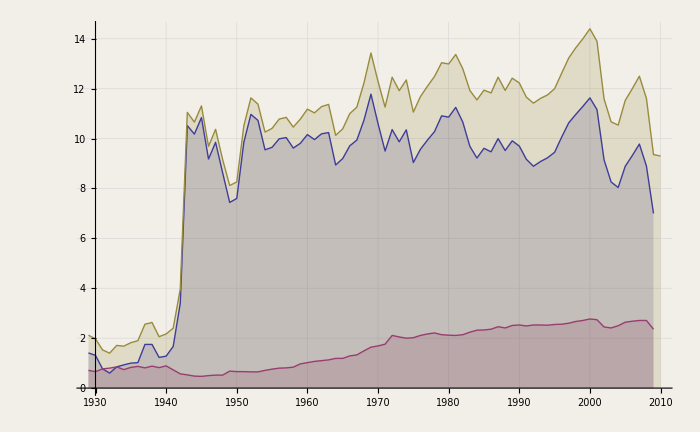

```mathematica
ListPlot[Table[data2⟦6;;,{1,i}⟧,{i,{6,7,8}}],Joined->True,Filling->Axis,GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],GrayLevel[0.8]],ImageSize->{700,432},Background->RGBColor[242/255,239/255,233/255]]
```

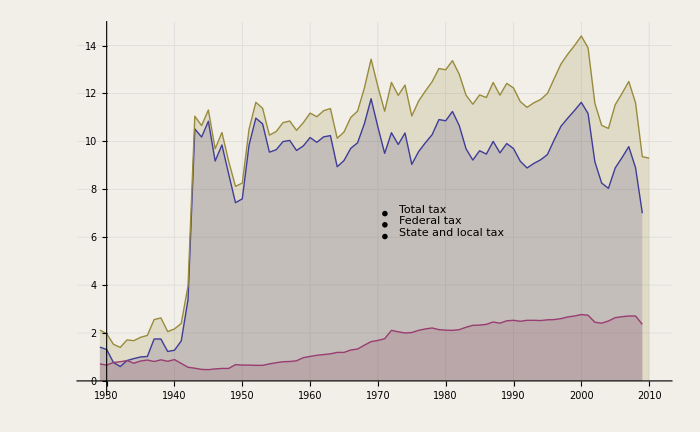
```mathematica
percentTax=-Graphics-;
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"taxpercent.svg"}],percentTax]
```

/Users/andrew/dc/web/d4t4.org/taxpercent.svg

```mathematica
taxPercentSmall=ListPlot[Table[data2⟦6;;,{1,i}⟧,{i,{6,7,8}}],Joined->True,Filling->Axis,GridLines->Automatic,GridLinesStyle->Directive[AbsoluteThickness[1],GrayLevel[0.8]],ImageSize->{80,60},Background->RGBColor[242/255,239/255,233/255],Axes->None]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"taxpercent_small.png"}],taxPercentSmall]
```

/Users/andrew/dc/web/d4t4.org/taxpercent_small.png